```mathematica
MatrixForm[Table[0,{i,2},{j,2}]]
```

(0 | 0
0 | 0)

```mathematica
H[kx_]:=({{μ, t +t Exp[I kx]}, {t+t Exp[-I kx], -μ}})
```

```mathematica
Eigensystem[H[kx]]
```

{{-ⅇ^(-(ⅈ kx)/2) √(t^2+2 ⅇ^(ⅈ kx) t^2+ⅇ^(2 ⅈ kx) t^2+ⅇ^(ⅈ kx) μ^2),ⅇ^(-(ⅈ kx)/2) √(t^2+2 ⅇ^(ⅈ kx) t^2+ⅇ^(2 ⅈ kx) t^2+ⅇ^(ⅈ kx) μ^2)},{{(ⅇ^((ⅈ kx)/2) (ⅇ^((ⅈ kx)/2) μ-√(t^2+2 ⅇ^(ⅈ kx) t^2+ⅇ^(2 ⅈ kx) t^2+ⅇ^(ⅈ kx) μ^2)))/((1+ⅇ^(ⅈ kx)) t),1},{(ⅇ^((ⅈ kx)/2) (ⅇ^((ⅈ kx)/2) μ+√(t^2+2 ⅇ^(ⅈ kx) t^2+ⅇ^(2 ⅈ kx) t^2+ⅇ^(ⅈ kx) μ^2)))/((1+ⅇ^(ⅈ kx)) t),1}}}

```mathematica
F[t_,μ_,kx_]:=1/(((ⅇ^((ⅈ kx)/2) (ⅇ^((ⅈ kx)/2) μ-√(t^2+2 ⅇ^(ⅈ kx) t^2+ⅇ^(2 ⅈ kx) t^2+ⅇ^(ⅈ kx) μ^2)))/((1+ⅇ^(ⅈ kx)) t))*Conjugate[(ⅇ^((ⅈ kx)/2) (ⅇ^((ⅈ kx)/2) μ-√(t^2+2 ⅇ^(ⅈ kx) t^2+ⅇ^(2 ⅈ kx) t^2+ⅇ^(ⅈ kx) μ^2)))/((1+ⅇ^(ⅈ kx)) t)]+1)
```

```mathematica
G[t_,μ_,kx_]:=((ⅇ^((ⅈ kx)/2) (ⅇ^((ⅈ kx)/2) μ-√(t^2+2 ⅇ^(ⅈ kx) t^2+ⅇ^(2 ⅈ kx) t^2+ⅇ^(ⅈ kx) μ^2)))/((1+ⅇ^(ⅈ kx)) t))*Conjugate[(ⅇ^((ⅈ kx)/2) (ⅇ^((ⅈ kx)/2) μ-√(t^2+2 ⅇ^(ⅈ kx) t^2+ⅇ^(2 ⅈ kx) t^2+ⅇ^(ⅈ kx) μ^2)))/((1+ⅇ^(ⅈ kx)) t)]/(((ⅇ^((ⅈ kx)/2) (ⅇ^((ⅈ kx)/2) μ-√(t^2+2 ⅇ^(ⅈ kx) t^2+ⅇ^(2 ⅈ kx) t^2+ⅇ^(ⅈ kx) μ^2)))/((1+ⅇ^(ⅈ kx)) t))*Conjugate[(ⅇ^((ⅈ kx)/2) (ⅇ^((ⅈ kx)/2) μ-√(t^2+2 ⅇ^(ⅈ kx) t^2+ⅇ^(2 ⅈ kx) t^2+ⅇ^(ⅈ kx) μ^2)))/((1+ⅇ^(ⅈ kx)) t)]+1)
```

```mathematica
Conjugate[Exp[I ]]
```

ⅇ^-ⅈ

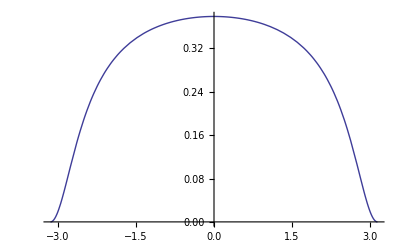

```mathematica
Plot[F[1,-0.5,kx],{kx,-Pi,Pi}]
```

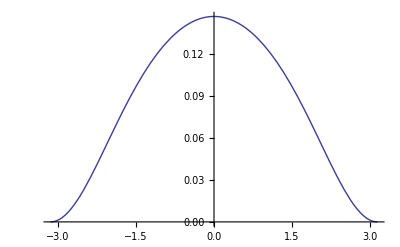

```mathematica
Plot[G[1,2,kx],{kx,-Pi,Pi}]
```

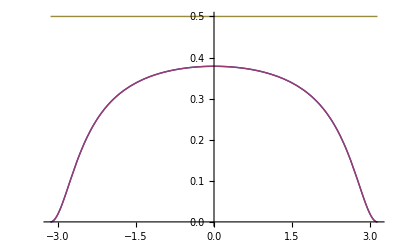

```mathematica
Plot[{F[1,-0.5,kx],G[1,0.5,kx],0.5},{kx,-Pi,Pi}]
```

```mathematica
COR=Table[NIntegrate[Exp[I kx (i-j)]F[1,0.1,kx],{kx,-Pi,Pi}]/2/Pi,{i,10},{j,10}];
```

```mathematica
MatrixForm[COR]
```

(0.718499-1.39395×10^-19 ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.0328524+0. ⅈ | -0.0168601+1.76697×10^-17 ⅈ | 0.00904997+0. ⅈ | -0.00498651-4.41744×10^-17 ⅈ | 0.00279516+2.42959×10^-17 ⅈ | -0.00158598-4.41744×10^-18 ⅈ | 0.000908081+9.60705×10^-17 ⅈ | -0.000523603-1.66122×10^-17 ⅈ
-0.0704569-6.37746×10^-20 ⅈ | 0.718499-1.39395×10^-19 ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.0328524+0. ⅈ | -0.0168601+1.76697×10^-17 ⅈ | 0.00904997+0. ⅈ | -0.00498651-4.41744×10^-17 ⅈ | 0.00279516+2.42959×10^-17 ⅈ | -0.00158598-4.41744×10^-18 ⅈ | 0.000908081+9.60705×10^-17 ⅈ
0.0328524+0. ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.718499-1.39395×10^-19 ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.0328524+0. ⅈ | -0.0168601+1.76697×10^-17 ⅈ | 0.00904997+0. ⅈ | -0.00498651-4.41744×10^-17 ⅈ | 0.00279516+2.42959×10^-17 ⅈ | -0.00158598-4.41744×10^-18 ⅈ
-0.0168601-1.76697×10^-17 ⅈ | 0.0328524+0. ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.718499-1.39395×10^-19 ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.0328524+0. ⅈ | -0.0168601+1.76697×10^-17 ⅈ | 0.00904997+0. ⅈ | -0.00498651-4.41744×10^-17 ⅈ | 0.00279516+2.42959×10^-17 ⅈ
0.00904997+0. ⅈ | -0.0168601-1.76697×10^-17 ⅈ | 0.0328524+0. ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.718499-1.39395×10^-19 ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.0328524+0. ⅈ | -0.0168601+1.76697×10^-17 ⅈ | 0.00904997+0. ⅈ | -0.00498651-4.41744×10^-17 ⅈ
-0.00498651+4.41744×10^-17 ⅈ | 0.00904997+0. ⅈ | -0.0168601-1.76697×10^-17 ⅈ | 0.0328524+0. ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.718499-1.39395×10^-19 ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.0328524+0. ⅈ | -0.0168601+1.76697×10^-17 ⅈ | 0.00904997+0. ⅈ
0.00279516-2.42959×10^-17 ⅈ | -0.00498651+4.41744×10^-17 ⅈ | 0.00904997+0. ⅈ | -0.0168601-1.76697×10^-17 ⅈ | 0.0328524+0. ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.718499-1.39395×10^-19 ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.0328524+0. ⅈ | -0.0168601+1.76697×10^-17 ⅈ
-0.00158598+4.41744×10^-18 ⅈ | 0.00279516-2.42959×10^-17 ⅈ | -0.00498651+4.41744×10^-17 ⅈ | 0.00904997+0. ⅈ | -0.0168601-1.76697×10^-17 ⅈ | 0.0328524+0. ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.718499-1.39395×10^-19 ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.0328524+0. ⅈ
0.000908081-9.82968×10^-17 ⅈ | -0.00158598+4.41744×10^-18 ⅈ | 0.00279516-2.42959×10^-17 ⅈ | -0.00498651+4.41744×10^-17 ⅈ | 0.00904997+0. ⅈ | -0.0168601-1.76697×10^-17 ⅈ | 0.0328524+0. ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.718499-1.39395×10^-19 ⅈ | -0.0704569-6.37746×10^-20 ⅈ
-0.000523603+1.87273×10^-17 ⅈ | 0.000908081-9.82968×10^-17 ⅈ | -0.00158598+4.41744×10^-18 ⅈ | 0.00279516-2.42959×10^-17 ⅈ | -0.00498651+4.41744×10^-17 ⅈ | 0.00904997+0. ⅈ | -0.0168601-1.76697×10^-17 ⅈ | 0.0328524+0. ⅈ | -0.0704569-6.37746×10^-20 ⅈ | 0.718499-1.39395×10^-19 ⅈ)

```mathematica
Eigenvalues[COR]
```

```mathematica
A={0.7730215975147838,0.6172435631621404,0.570993914034307,0.5511393613941914,0.5406872201919152,0.5343867676960311,0.5303951446490893,0.5277953982743426,0.5261636640141955,0.5252586013362639};
```

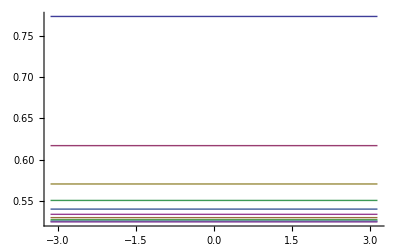

```mathematica
Plot[A,{x,-Pi,Pi},]
```

```mathematica
CORB=Table[NIntegrate[Exp[I kx (i-j)]G[1,0.1,kx],{kx,-Pi,Pi}]/2/Pi,{i,10},{j,10}];
```

```mathematica
Eigenvalues[CORB]
```

```mathematica
B={0.47474139866378673,0.47383633598583946,0.47220460172567985,0.4696048553509301,0.46561323230399565,0.4593127798081103,0.44886063860582104,0.4290060859656718,0.3827564368378005,0.22697840248511664}
```

{0.474741,0.473836,0.472205,0.469605,0.465613,0.459313,0.448861,0.429006,0.382756,0.226978}

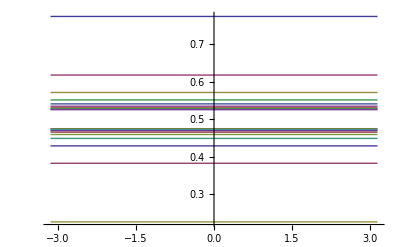

```mathematica
Plot[{A,B},{kx,-Pi,Pi}]
```

{0.951869-3.05489×10^-19 ⅈ,0.85778+7.50438×10^-19 ⅈ,0.777564-1.03662×10^-18 ⅈ,0.722468+6.94832×10^-19 ⅈ,0.685962-4.78696×10^-19 ⅈ,0.661502-2.25758×10^-19 ⅈ,0.644924+1.39512×10^-19 ⅈ,0.633767-5.88911×10^-19 ⅈ,0.626589-9.47165×10^-21 ⅈ,0.622565-3.33782×10^-19 ⅈ}

{0.377435-6.00129×10^-17 ⅈ,0.373411-2.19161×10^-17 ⅈ,0.366233-1.19456×10^-17 ⅈ,0.355076-1.89162×10^-18 ⅈ,0.338498+7.483×10^-18 ⅈ,0.314038+1.67491×10^-17 ⅈ,0.277532+2.18461×10^-17 ⅈ,0.222436+1.71793×10^-17 ⅈ,0.14222+8.09332×10^-18 ⅈ,0.0481308+2.87832×10^-17 ⅈ}

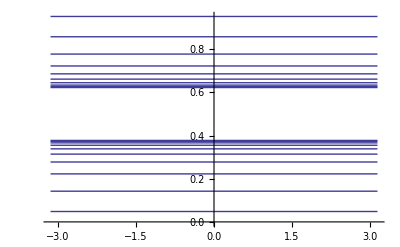

```mathematica
A=Eigenvalues[Table[NIntegrate[Exp[I kx (i-j)]F[1,0.5,kx],{kx,-Pi,Pi}]/2/Pi,{i,10},{j,10}]]
B=Eigenvalues[Table[NIntegrate[Exp[I kx (i-j)]G[1,0.5,kx],{kx,-Pi,Pi}]/2/Pi,{i,10},{j,10}]]
Plot[Re[{A,B}],{kx,-Pi,Pi}]
```